1. Cari solusi untuk x dan y dari persamaan a dan b dengan wolfram mathematica, lalu cari nilai limit
dari c,d dan e dengan menggunakan metode pendekatan dan perintah limit dalam wolfram mathematica
kemudian sertakan gambar dalam penjelasan!(Hint: Gunakan Table)

a. ax^2+bx^3+cx^4=0 dengan nilai a, b, c adalah 3 digit terakhir NPM kalian
    Ditanya: Nilai x?
    Jawab: 
    3 digit terakhir NPM saya adalah 136 sehingga a=1, b=3, c=6
    Maka persamaan yang ingin diselesaikan adalah x^2+3 x^3+6 x^4=0
    Dalam penulisannya di Wolfram Mathematica, gunakanlah x^2+3 x^3+6 x^4==0
    
    Mari kita cari solusi dari persamaan ini.
    Untuk menyelesaikan suatu persamaan dan mendapatkan nilai, gunakan fungsi Solve.
    	Solve[Persamaan, {Nilai yang dicari}]  
    Kemudian setelah mengetik fungsi, tahan shift dan tekan enter.

```mathematica
Solve[x^2+3 x^3+6 x^4==0, {x}]
```

{{x→0},{x→0},{x→1/12 (-3-ⅈ √15)},{x→1/12 (-3+ⅈ √15)}}

Sehingga kita mendapatkan hasil yang kita inginkan yaitu nilai x, dimana nilai x tersebut yaitu x=0,x=0,x=1/12 (-3-ⅈ √15),x=1/12 (-3+ⅈ √15)

--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
b. 2x - y = 3
    x + 4y = -2
    Ditanya: Nilai x dan y?
    Jawab:
    Mari kita cari solusi dari kedua persamaan tersebut.
    Sekali lagi untuk menyelesaikan persamaan, gunakan fungsi Solve namun dengan sedikit modifikasi.
    Ingat untuk mengganti = dengan ==
    	Solve[Persamaan 1 && Persamaan 2, {Nilai yang dicari}]
    Kemudian setelah mengetik fungsi, tahan shift dan tekan enter. Prinsip ini berlaku untuk semua fungsi yang kita ingin Wolfram selesaikan.

```mathematica
Solve[2x+y==0 && x+4y==-2, {x,y}]
```

{{x→2/7,y→-4/7}}

Sehingga kita mendapatkan hasil yang kita inginkan yaitu nilai x dan y, dimana nilai x tersebut adalah x=2/7 dan y=-4/7 

--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

c. lim_(x→ (π/4)^-)  tan 2x
    Ditanya: Nilai limit fungsi?
    Jawab:
Mari kita cari limit dari fungsi tersebut.
Berbeda dengan soal-soal sebelumnya, disini karena limit merupakan fungsi kedua setelah tan 2x sehingga ada 2 fungsi, maka fungsi tan 2x perlu didefiniskan.
Untuk mendefiniskan suatu fungsi, gunakan format fungsi di bawah
	p [x_] := Fungsi

p ini merupakan variabel, sehinnga bukan suatu keharusan, variabel ini sebenarnya bebas
Kemudian tahan shift dan tekan enter untuk mendefinisikan p[x] sebagai fungsi yang diinginkan.

Sekarang karena satu dari 2 fungsi telah terdefinisikan, maka kita tersisa dengan 1 fungsi, sehingga kita dapat menyelesaikannya.

Perhatikan soal, limit tersebut memetakan x→(π/4)^- atau kita dapat definisikan secara bahasa sebagai x mendekati π/4 atau 45° dari kiri (- mewakili dari kiri, dan sebaliknya + mewakili dari kanan)

	catatan: untuk membuat konstanta seperti π ini, dapat diakses melalui window pada bagian atas yang bernama “Palettes” dan memilih salah satu dari Basic Math Assistant atau Classroom 	
	Assistant lalu tinggal mencari yang diinginkan kemudian diklik. Adapun cara lain yaitu dengan mengetik Pi. Ini sudah merepresentasikan π.

Dari situ, mari kita selesaikan menggunakan distribusi nilai fungsi dari 0 hingga sebelum 45°, mari kita ambil sampai dengan 42°.
Angka ini mebenarnya bebas, silakan jika ingin mencoba angka lain.
Mari kita buat tabel disribusi nilai dari 0° hingga 44° dengan jarak 11°.
Untuk membuat tabel distribusi nilai, gunakan format fungsi di bawah
	Table [ {x, p[x]}, {x, Nilai awal yang ingin digunakan, Nilai batas yang ingin digunakan, Nilai jarak distribusi dari nilai awal hingga nilai batas} ] // TableForm
Sekarang mari aplikasikan kedua prinsip tersebut untuk menjawab soal. Gunakan kedua sistem tersebut kemudian tahan shift dan tekan enter.

```mathematica
p[x_]:=Tan[2x]
Table[{x,p[x]},{x,0,44°,11°}]//TableForm
```

0 | 0
11 ° | Tan[22 °]
22 ° | Tan[44 °]
33 ° | Cot[24 °]
44 ° | Cot[2 °]

Dari tabel diatas, dapat dilihat bahwa fungsi menuju cot [0] sehingga kita mendapatkan solusi dari   lim_(x→ (π/4)^-)  tan 2x   yaitu cot [0] atau 1/(tan [0]) = 1/0 = ∞
--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

d. lim_(x→ ∞) (x-ⅇ)/(x+2ⅇ)
    Ditanya: Nilai limit fungsi?
    Jawab:
Mari kita jawab soal tersebut.  Berbeda dengan sebelumnya, limit menuju suatu angka yang dapat dihitung, soal ini menuju ∞ atau tak hingga.
Sehingga untuk menyelesaikan soal seperti ini, mari gunakan angka 100 hingga 1000. Kenapa? Agar memproyeksikan perubahan angka saat semakin besar tanpa batas (menuju tak hingga).
Gunakan cara yang sama dengan sebelumnya.
Namun mungkin ada kebingungan bagaimana memasukkan konstanta. Langkah yang dapat dilakukan sama dengan cara yang sudah dikatakan dalam soal sebelumnya. Jika tidak ingin melakukan itu, terdapat alternatif, yaitu dengan mengetik E. Ini sudah merepresentasikan ⅇ.

```mathematica
q[x_]:=(x-ⅇ)/(x+2ⅇ)
```

```mathematica
Table[{x,q[x]},{x,100,1000,50}]//TableForm
```

100 | (100-ⅇ)/(100+2 ⅇ)
150 | (150-ⅇ)/(150+2 ⅇ)
200 | (200-ⅇ)/(200+2 ⅇ)
250 | (250-ⅇ)/(250+2 ⅇ)
300 | (300-ⅇ)/(300+2 ⅇ)
350 | (350-ⅇ)/(350+2 ⅇ)
400 | (400-ⅇ)/(400+2 ⅇ)
450 | (450-ⅇ)/(450+2 ⅇ)
500 | (500-ⅇ)/(500+2 ⅇ)
550 | (550-ⅇ)/(550+2 ⅇ)
600 | (600-ⅇ)/(600+2 ⅇ)
650 | (650-ⅇ)/(650+2 ⅇ)
700 | (700-ⅇ)/(700+2 ⅇ)
750 | (750-ⅇ)/(750+2 ⅇ)
800 | (800-ⅇ)/(800+2 ⅇ)
850 | (850-ⅇ)/(850+2 ⅇ)
900 | (900-ⅇ)/(900+2 ⅇ)
950 | (950-ⅇ)/(950+2 ⅇ)
1000 | (1000-ⅇ)/(1000+2 ⅇ)

Di sini dapat dilihat bahwa kita tidak dapat menarik kesimpulan apa pun karena ⅇ tetap bernilai sama. Maka kita perlu definisikan ulang fungsi dengan pertama mendefinisikan nilai ⅇ.
Untuk mengetahui nilai suatu konstanta atau tetapan seperti ⅇ, gunakan fungsi di bawah.
	N[konstanta yang ingin dicari]

```mathematica
N[e]
```

2.71828

Setelah kita mendapatkan nilai ⅇ, definisikan ulang fungsi dan kerjakan ulang dengan cara yang sama.

```mathematica
q[x_]:=(x-2.71828)/(x+5.43656)
```

```mathematica
Table[{x,q[x]},{x,100,1000,50}]//TableForm
```

100 | 0.922656
150 | 0.947536
200 | 0.960305
250 | 0.968075
300 | 0.973301
350 | 0.977057
400 | 0.979886
450 | 0.982094
500 | 0.983866
550 | 0.985318
600 | 0.986531
650 | 0.987558
700 | 0.98844
750 | 0.989205
800 | 0.989875
850 | 0.990467
900 | 0.990993
950 | 0.991465
1000 | 0.991889

Sekarang kita dapat menarik sebuah kesimpulan, yaitu semakin nilai x membesar menuju tak hingga, semakin q[x] menuju 1, sehingga nilai limit dari (x-ⅇ)/(x+2ⅇ) adalah 1.
--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
e. lim_(x→ 0) x^4 sin^2(1/x)
    Ditanya: Nilai limit fungsi?
    Jawab:
Mari kita jawab soal ini. Cara mengerjakannya serupa dengan soal-soal sebelumnya, namun yang perlu diperhatikan di sini adalah x menuju 0. 
Tidak ada pengkhususan - (dari kiri) atau + (kanan), sehingga kita perlu mencoba dari kedua arah.
Seperti biasa definisikan fungsi terlebih dahulu kemudian buatlah tabel yang mendekati 0 dari kiri dan dari kanan. Di sini diambil contoh dari -1 hingga -0.1 dan 1 hingga 0.1.
Sekali lagi, angka-angka ini bebas.

```mathematica
r[x_]:= x^4 sin^2(1/x)
```

```mathematica
Table[{x,r[x]},{x,-1,-0.1,0.1}]//TableForm
```

-1. | 0.708073
-0.9 | 0.526954
-0.8 | 0.368874
-0.7 | 0.235276
-0.6 | 0.128412
-0.5 | 0.0516764
-0.4 | 0.00916912
-0.3 | 0.000294161
-0.2 | 0.00147126
-0.1 | 0.0000295959

```mathematica
Table[{x,r[x]},{x,1,0.1,-0.1}]//TableForm
```

1. | 0.708073
0.9 | 0.526954
0.8 | 0.368874
0.7 | 0.235276
0.6 | 0.128412
0.5 | 0.0516764
0.4 | 0.00916912
0.3 | 0.000294161
0.2 | 0.00147126
0.1 | 0.0000295959

Dari sini dapat terlihat bahwa distribusi nilai fungsi r[x] saat x dimasukkan akan semakin mendekati 0 dari kedua arah. Sehingga limit dari x^4 sin^2(1/x) adalah 0.
--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
2. Didefinisikan

```mathematica
2ax+b, x < - 5
   f(x)= 6b           , -5 ≤ x < 1
		3               , x ≥ 1
```

Tentukan nilai dari a dan b sedemikian sehingga fungsi f kontinu pada seluruh domainnya! Buktikan
kekontinuannya dengan definisi dan perintah Wolfram Mathematica kemudian plot juga grafiknya
dengan nilai a dan b yang benar!

Ditanya: 
a) nilai a dan b sehingga kontinu pada seluruh domain, 
b) buktikan menggunakan definisi kekontinuannya,
c) grafik dengan nilai a dan b yang benar.

Jawab:
Pertama mari kita definiskan fungsi tersebut.
Kita perlu melihat fungsi ini, berbeda dengan fungsi-fungsi sebelumnya, fungsi ini merupakan suatu fungsi yang memiliki pemetaan berbeda untuk domain-domain tertentu.
Fungsi ini dikenal sebagai fungsi Piecewise.
Mari kita definisikan fungsi ini.

```mathematica
f[x_]:=Piecewise[{{2a x+b,x<-5},{6b,-5≤x<1},{3,x≥1}}]
```

Dengan ini, fungsi f(x) telah terdefinisi. Mari kita lanjut ke soal.

a) Untuk mencari nilai a dan b, kita dapat memanfaatkan prinsip limit. Kenapa? Karena agar suatu fungsi kontinu, fungsi tersebut harus terdefinisi dalam fungsi dan dalam limitnya.
Agar suatu fungsi kontinu, maka limit kiri harus sama dengan limit kanan. Sehingga yang perlu kita lakukan adalah seperti berikut.

```mathematica
Solve[Limit[f[x],x->-5,Direction->1]==Limit[f[x],x->-5,Direction->-1]&&Limit[f[x],x->1,Direction->1]==Limit[f[x],x->1,Direction->-1],{a,b}]
```

{{a→-1/4,b→1/2}}

catatan: Direction ini mewakilkan limit adalah limit kiri (-> 1) dan limit kanan (-> -1)

Dengan ini, kita mendapatkan nilai a dan b yaitu a=-1/4 dan b=1/2.
Selanjutnya, untuk menjawab soal-soal selanjutnya, kita definisikan variabel tersebut. Sehingga saat menggunakan variabel tersebut, secara otomatis sudah sesuai nilai yang kita inginkan.

```mathematica
a=-1/4
```

-1/4

```mathematica
b=1/2
```

1/2

--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
b) Untuk membuktikan kekontinuan, telah dibilang bahwa limit kiri sama dengan limit kanan, sehingga kita hanya perlu mengecek titik-titik kekontinuan yaitu -5 dan 1.
Untuk mengecek apakah 2 buah persamaan sama, gunakan format fungsi berikut.
	Persamaan 1 == Persamaan 2
Dari sini, yang akan muncul apabila nilai sama, “True”. Sedangkan jika nilai tidak sama, “False”.

```mathematica
Limit[f[x],x-> -5, Direction-> 1]== Limit[f[x], x-> -5, Direction-> -1]
```

True

Di sini, terlihat bahwa limit kiri sudah sama dengan limit kanan, sehinga x=-5 kontinu.

```mathematica
Limit[f[x], x->1, Direction->1]==Limit[f[x], x-> 1, Direction -> -1]
```

True

Di sini, terlihat bahwa limit kiri sudah sama dengan limit kanan, sehingga x=1 kontinu
--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

c) Mari kita gambarkan fungsi piecewise ini. Untuk menggambarkan suatu fungsi, gunakan format fungsi berikut.
	Plot[Fungsi, {Variabel bidang yang diinginkan, Nilai bawah variabel bidang, Nilai atas variabel bidang}]
    Kemudian dapat dilengkapi lagi dengan PlotRange. Mengapa? Karena grafik hanya terfokus pada satu bidang variabel atau dalam contoh x. Dengan ini, grafik dapat lebih seperti keinginan.
    	Misal: Plot[Fungsi, {x, -2, 2}], PlotRange -> {Nilai bawah y, Nilai atas y}]
    Fungsi ini juga dapat dilengkapi dengan PlotStyle, untuk memodifikasi warna dan ketebalan grafik yang diinginkan.
    	Misal: Plot[Fungsi, {x, -2, 2}, PlotRange -> {-2, 2}, PlotStyle -> {Warna Grafik, Thickness[Tingkat Ketebalan]}]
    
    
    Mari aplikasikan untuk menjawab soal, di sini akan digunakan warna ungu yang sedikit tebal.

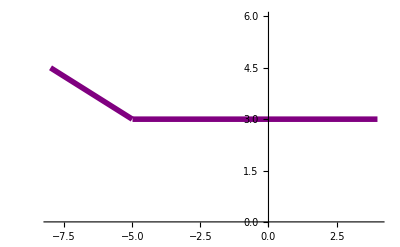

```mathematica
Plot[f[x],{x,-8,4}, PlotRange-> {0,6},PlotStyle-> {Purple, Thickness[0.01]}]
```

--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
3. Apakah fungsi f berikut kontinu di x = 2 ? Jika tidak, jelaskan alasannya.

a. f(x) = 4 x^2-2x+12
    Ditanya: Kekontinuan pada x=2?
    Jawab:
    Kerjakan menggunakan cara yang sama dengan soal sebelumnya. Namun kita gunakan pendekatan lain, yaitu tanpa mengurai fungsinya lagi dan langsung masuk ke dalam fungsi.

```mathematica
Limit[4 x^2-2x+12, x-> 2, Direction-> 1]==Limit[4 x^2-2x+12, x->2, Direction -> -1]
```

True

Karena limit kiri sama dengan limit kanan, maka fungsi ini kontinu pada x = 2.
--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

b. f(x) = 8/(x-2)
    Ditanya: Kekontinuan pada x=2?
    Jawab:
    Kerjakan menggunakan cara yang sama dengan soal sebelumnya.

```mathematica
Limit[8/(x-2), x-> 2, Direction-> 1]==Limit[8/(x-2), x-> 2, Direction-> -1]
```

False

Karena limit kiri tidak sama dengan limit kanan, fungsi ini tidak memiliki limit pada x = 2 sehingga f(x) diskontinu pada x = 2.
--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

4. Carilah sebuah fungsi yang memiliki nilai limit di suatu titik, namun nilai limit di titik tersebut tersebut tidak sama dengan nilai fungsinya. Kemudian plot fungsinya.

    Diketahui: Fungsi yang memiliki limit di suatu titik namun limit di titik tersebut tidak sama dengan nilai fungsi
    Ditanya: Fungsi tersebut dan grafiknya?
    Jawab:
    Soal ini memiliki kebebasan untuk dijawab. Cara mudah yang dapat dilakukan adalah mencari suatu titik yang akan memetakan fungsi pada nilai ∞

```mathematica
z[x_]:=(x^2-25)/(x-5)
```

```mathematica
Limit[z[x],x->5,Direction->1]==Limit[z[x],x->5,Direction->-1]
```

True

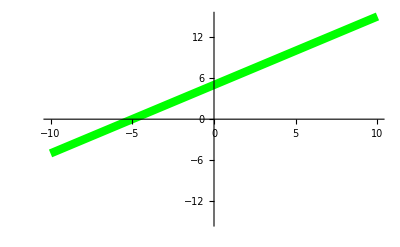

```mathematica
Plot[z[x],{x,-10,10},PlotRange->{-15,15},PlotStyle-> {Green, Thickness[0.015]}]
```

Sehingga kita mendapatkan contoh fungsi dan grafiknya dari yang diminta oleh soal.